## Bootstrapped EWS for Brachionus

## Setup

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* Job number *)
jobNum=6546;
```

```mathematica
(* Data directory *)
dataDir="hagrid/fussmann_ews/Jobs/job-"<>ToString[jobNum]<>"/";
```

```mathematica
(* Import parameters used *)
pars=Import[dataDir<>"pars.txt","Data"];
```

```mathematica
pars//TableForm
```

span | rw | ham_length | ham_offset | w_cutoff | sweep | block_size | bs_type | n_samples
80 | 1 | 80 | 0.5 | 1 | true | 40 | Circular | 100

```mathematica
(* EWS data *)
ewsRaw=Import[dataDir<>"ews_intervals.csv"];
```

```mathematica
(* bootstraped power spectrumdata *)
pspecBootRaw=Import[dataDir<>"/pspec.csv"];
```

```mathematica
(* power spectrum data *)
pspecChlorRaw=Import["data_export/pspec_chlor.csv"];
pspecBrachRaw=Import["data_export/pspec_brach.csv"];
```

```mathematica
deltaVals=Union[ewsRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

### Construct power spectrum data

```mathematica
pspecBootRaw[[2]]
```

{0.04,Brachionus,1,-3.14159,0.084653}

```mathematica
(* bootstrapped data *)
sample=4;
pspecsBootBrach=Table[Cases[pspecBootRaw,{delta,"Brachionus",sample,_,_}][[;;,{4,5}]],{delta,deltaVals}];
pspecsBootChlor=Table[Cases[pspecBootRaw,{delta,"Chlorella",sample,_,_}][[;;,{4,5}]],{delta,deltaVals}];
```

```mathematica
(* original power spectra *)
pspecsBrach=Table[Cases[pspecBrachRaw,{delta,_,_}][[;;,{2,3}]],{delta,deltaVals}];
pspecsChlor=Table[Cases[pspecChlorRaw,{delta,_,_}][[;;,{2,3}]],{delta,deltaVals}];
```

```mathematica
deltaVals
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### General figure parameters

```mathematica
(* Figure params *)
TMBcolours=ColorData[97,"ColorList"];
imgs=400;
colChlor=Black;
colBrach=Darker[TMBcolours[[5]],0.15];
```

```mathematica
aRatio=0.25; (* aspect ratio *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterSize=12;
ltb=0.005; (* line thickness for bifurcation *)
lt=0.005; (* line thickness *)
ls=9; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Plot Playground

```mathematica
deltaVals
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* Delta values approaching h1 *)
deltaH1={0.04,0.07,0.12,0.32,0.64};
deltaH1index=Position[deltaVals,#]&/@deltaH1//Flatten;
```

```mathematica
(* Delta values approahing h2 *)
deltaH2={1.37,1.24,1.17,0.95,0.69};
deltaH2index=Position[deltaVals,#]&/@deltaH2//Flatten;
```

### Power spectra from original series

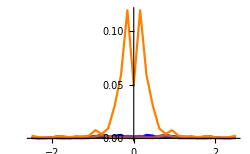

```mathematica
(* Chlorella approach H1 *)
ListLinePlot[Table[pspecsChlor[[i]],{i,deltaH1index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}]]
```

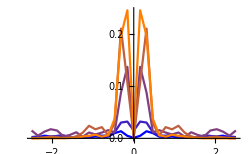

```mathematica
(* Chlorella approach H2 *)
ListLinePlot[Table[pspecsChlor[[i]],{i,deltaH2index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}]]
```

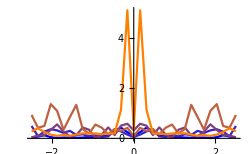

```mathematica
(* Brachionus approach H1 *)
ListLinePlot[Table[pspecsBrach[[i]],{i,deltaH1index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}]]
```

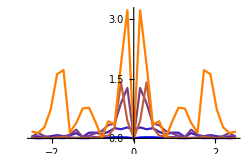

```mathematica
(* Brachionus approach H2 *)
ListLinePlot[Table[pspecsBrach[[i]],{i,deltaH2index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}]]
```

### Power spectra from bootstrapped series

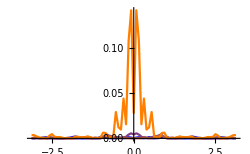

```mathematica
(* Chlorella approach H1 *)
ListLinePlot[Table[pspecsBootChlor[[i]],{i,deltaH1index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}]]
```

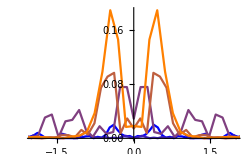

```mathematica
(* Chlorella approach H2 *)
ListLinePlot[Table[pspecsBootChlor[[i]],{i,deltaH2index}],
ImageSize->250,
PlotRange->{{-2,2},All},
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}]]
```

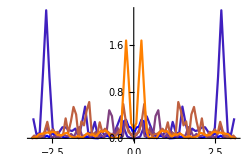

```mathematica
(* Brachionus approach H1 *)
ListLinePlot[Table[pspecsBootBrach[[i]],{i,deltaH1index}],
ImageSize->250,
PlotRange->All,
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH1]-1)}]]
```

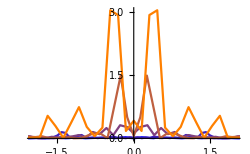

```mathematica
(* Brachionus approach H2 *)
ListLinePlot[Table[pspecsBootBrach[[i]],{i,deltaH2index}],
ImageSize->250,
PlotRange->{{-2,2},All},
PlotStyle->Table[colFun1[i],{i,0,1,1/(Length[deltaH2]-1)}]]
```

### Bifurcation data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
bifPtsChlor=Table[DeleteCases[bifPtsChlor[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsChlor]}];
bifPtsBrach=Table[DeleteCases[bifPtsBrach[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsBrach]}];
```

## Bifurcation diagram

```mathematica
deltaVals=Union[ewsRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.95,1.17,1.24,1.37}

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=0.32;
expBif1b=0.64;
expBif2=1.16;
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* Legend *)
legend=LineLegend[{colChlor,colBrach},{Style["Chlorella Vulgaris",ls],Style["Brachionus Calyciflorus",ls]},Spacings->{0,0.2}]
```

```mathematica
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[ltb]},{i,1,Length[bifPtsChlor]}],
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,6}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,6]*1000000,Range[0,6]}],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False,
PlotLegends->Placed[legend,Scaled[{0.78,0.85}]],
Epilog->{Directive[{Black}],
Line[Table[{Scaled[{0,-0.05},{deltaVals[[i]],0}],
Scaled[{0,0.05},{deltaVals[[i]],0}]},{i,1,Length[deltaVals]}]],
Directive[{Black}],Text[Style["a",labelLetterSize,Bold],labelLetterPos]}]
```

-Graphics-

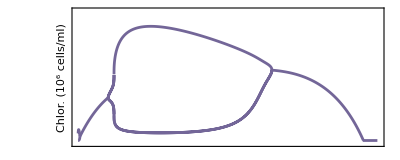

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-64/40,64}},
PlotStyle->Table[{colBrach,Thickness[ltb]},{i,1,Length[bifPtsBrach]}],
LabelStyle->ls,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlor. (10^6 cells/ml)",White],"Brach. (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4,
PlotRangeClipping->False]
```

## Plots of EWS against delta

### Variance and Smax for Chlorella

```mathematica
colVar=TMBcolours[[2]];
colSmax=TMBcolours[[3]];
```

```mathematica
(* line legend *)
legend=LineLegend[{colVar,colSmax},{"Variance","S_max"},Spacings->{0,0},LabelStyle->(ls-1)]
```

```mathematica
(* Index of EWS of interest *)
indexVar=Position[ewsRaw[[1]],"Variance"][[1,1]];
indexSmax=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals for variance of Chlorella *)
lowerVar=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperVar=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanVar=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for smax of Chlorella *)
lowerSmax=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSmax=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSmax=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

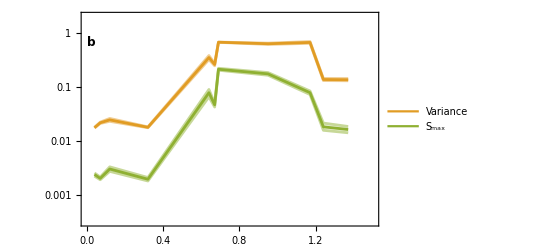

```mathematica
varSmaxPlotChlor=ListLinePlot[{lowerVar,upperVar,meanVar,lowerSmax,upperSmax,meanSmax},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2},6->{4},6->{5}}},
PlotRange->{{0,1.5},{10^(-3.5),2}},
PlotStyle->{{Lighter[colVar,0.5],Thickness[lt]},{Lighter[colVar,0.5],Thickness[lt]},{colVar,Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{colSmax,Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.9,0.85}]],
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
]
```

### Variance and Smax for Brachionus

```mathematica
colVar=TMBcolours[[2]];
colSmax=TMBcolours[[3]];
```

```mathematica
(* Index of EWS of interest *)
indexVar=Position[ewsRaw[[1]],"Variance"][[1,1]];
indexSmax=Position[ewsRaw[[1]],"Smax"][[1,1]];
```

```mathematica
(* Extract confidence intervals for variance of Chlorella *)
lowerVar=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperVar=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanVar=Cases[ewsRaw[[2;;,{1,2,3,indexVar}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for smax of Chlorella *)
lowerSmax=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSmax=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSmax=Cases[ewsRaw[[2;;,{1,2,3,indexSmax}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

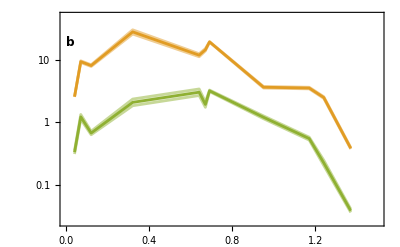

```mathematica
varSmaxPlotBrach=ListLinePlot[{lowerVar,upperVar,meanVar,lowerSmax,upperSmax,meanSmax},
LabelStyle->ls,
ScalingFunctions->"Log",
InterpolationOrder->1,
Filling->{{3->{1},3->{2},6->{4},6->{5}}},
PlotRange->{{0,1.5},{10^(-1.6),10^(1.7)}},
PlotStyle->{{Lighter[colVar,0.5],Thickness[lt]},{Lighter[colVar,0.5],Thickness[lt]},{colVar,Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{Lighter[colSmax,0.5],Thickness[lt]},{colSmax,Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"",""}},
FrameTicks->{{{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10},{100,100}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["b",labelLetterSize,Bold],labelLetterPos]}
]
```

### Lag-1 AC

```mathematica
ewsIndex=Position[ewsRaw[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanSeriesC=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Brachionus *)
lowerSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanSeriesB=Cases[ewsRaw[[2;;,{1,2,3,ewsIndex}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Compute composite EWS *)
lowerSeriesComp=Transpose[{lowerSeriesB[[;;,1]],Mean[{Standardize[lowerSeriesB[[;;,2]]],Standardize[lowerSeriesC[[;;,2]]]}]}];
upperSeriesComp=Transpose[{upperSeriesB[[;;,1]],Mean[{Standardize[upperSeriesB[[;;,2]]],Standardize[upperSeriesC[[;;,2]]]}]}];
meanSeriesComp=Transpose[{meanSeriesB[[;;,1]],Mean[{Standardize[meanSeriesB[[;;,2]]],Standardize[meanSeriesC[[;;,2]]]}]}];
```

```mathematica
ac1PlotChlor=ListLinePlot[{lowerSeriesC,upperSeriesC,meanSeriesC},
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{{Lighter[colChlor,0.5],Thickness[lt]},{Lighter[colChlor,0.5],Thickness[lt]},{colChlor,Thickness[lt]}},
Filling->{{3->{1},3->{2}}},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-0.8,0.8,0.4],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["d",labelLetterSize,Bold],labelLetterPos]}];
```

```mathematica
ac1PlotBrach=ListLinePlot[{lowerSeriesB,upperSeriesB,meanSeriesB},
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,1.5},{-0.5,1}},
PlotStyle->{{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],Lighter[colBrach,0.5]},{Thickness[lt],colBrach}},
Filling->{{3->{1},3->{2}}},
Frame->{{False,True},{True,True}},
FrameLabel->{{"","Lag-1 AC"},{"",""}},
FrameTicks->{{None,Range[-0.8,0.8,0.4]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
ImageSize->imgs];
```

### AIC weights Chlorella

```mathematica
(* figure colours *)
aicCols=TMBcolours[[{15,8,6}]]
```

{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[1, 0.75, 0],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
(* line legend *)
legend=LineLegend[aicCols,{"w_fold","w_flip","w_null"},Spacings->{0,-0.2},LabelStyle->(ls-1)]
```

```mathematica
(* Index of EWS of interest *)
indexFold=Position[ewsRaw[[1]],"AIC fold"][[1,1]];
indexHopf=Position[ewsRaw[[1]],"AIC hopf"][[1,1]];
indexNull=Position[ewsRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerFoldC=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperFoldC=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanFoldC=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerHopfC=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperHopfC=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanHopfC=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerNullC=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Chlorella","Lower",_}][[;;,{1,4}]];
upperNullC=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Chlorella","Upper",_}][[;;,{1,4}]];
meanNullC=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Chlorella","Mean",_}][[;;,{1,4}]];
```

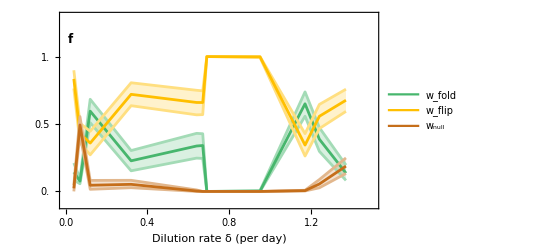

```mathematica
aicPlotChlor=ListLinePlot[{lowerFoldC,upperFoldC,meanFoldC,lowerHopfC,upperHopfC,meanHopfC,lowerNullC,upperNullC,meanNullC},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}},
PlotRange->{{0,1.5},{-0.1,1.3}},
PlotStyle->{{Lighter[aicCols[[1]],0.5],Thickness[lt]},{Lighter[aicCols[[1]],0.5],Thickness[lt]},{aicCols[[1]],Thickness[lt]},
{Lighter[aicCols[[2]],0.5],Thickness[lt]},{Lighter[aicCols[[2]],0.5],Thickness[lt]},{aicCols[[2]],Thickness[lt]},
{Lighter[aicCols[[3]],0.5],Thickness[lt]},{Lighter[aicCols[[3]],0.5],Thickness[lt]},{aicCols[[3]],Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
PlotLegends->Placed[legend,Scaled[{0.9,0.8}]],
Epilog->{Directive[{Black}],Text[Style["f",labelLetterSize,Bold],labelLetterPos]}]
```

### AIC weights Brachionus

```mathematica
(* Index of EWS of interest *)
indexFold=Position[ewsRaw[[1]],"AIC fold"][[1,1]];
indexHopf=Position[ewsRaw[[1]],"AIC hopf"][[1,1]];
indexNull=Position[ewsRaw[[1]],"AIC null"][[1,1]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerFoldB=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperFoldB=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanFoldB=Cases[ewsRaw[[2;;,{1,2,3,indexFold}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerHopfB=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperHopfB=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanHopfB=Cases[ewsRaw[[2;;,{1,2,3,indexHopf}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

```mathematica
(* Extract confidence intervals for Chlorella *)
lowerNullB=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Brachionus","Lower",_}][[;;,{1,4}]];
upperNullB=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Brachionus","Upper",_}][[;;,{1,4}]];
meanNullB=Cases[ewsRaw[[2;;,{1,2,3,indexNull}]],{_,"Brachionus","Mean",_}][[;;,{1,4}]];
```

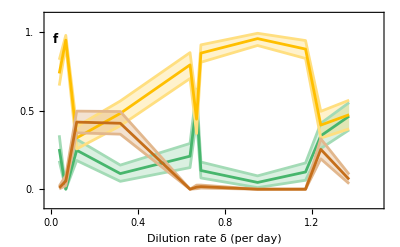

```mathematica
aicPlotBrach=ListLinePlot[{lowerFoldB,upperFoldB,meanFoldB,lowerHopfB,upperHopfB,meanHopfB,lowerNullB,upperNullB,meanNullB},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Lighter[aicCols[[1]],0.5],Thickness[lt]},{Lighter[aicCols[[1]],0.5],Thickness[lt]},{aicCols[[1]],Thickness[lt]},
{Lighter[aicCols[[2]],0.5],Thickness[lt]},{Lighter[aicCols[[2]],0.5],Thickness[lt]},{aicCols[[2]],Thickness[lt]},
{Lighter[aicCols[[3]],0.5],Thickness[lt]},{Lighter[aicCols[[3]],0.5],Thickness[lt]},{aicCols[[3]],Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["f",labelLetterSize,Bold],labelLetterPos]}]
```

### AIC weights: Composite

```mathematica
(* Compute composite EWS *)
lowerFoldComp=Transpose[{lowerFoldB[[;;,1]],Mean[{lowerFoldB[[;;,2]],lowerFoldC[[;;,2]]}]}];
upperFoldComp=Transpose[{upperFoldB[[;;,1]],Mean[{upperFoldB[[;;,2]],upperFoldC[[;;,2]]}]}];
meanFoldComp=Transpose[{meanFoldB[[;;,1]],Mean[{meanFoldB[[;;,2]],meanFoldC[[;;,2]]}]}];
```

```mathematica
(* Compute composite EWS *)
lowerHopfComp=Transpose[{lowerHopfB[[;;,1]],Mean[{lowerHopfB[[;;,2]],lowerHopfC[[;;,2]]}]}];
upperHopfComp=Transpose[{upperHopfB[[;;,1]],Mean[{upperHopfB[[;;,2]],upperHopfC[[;;,2]]}]}];
meanHopfComp=Transpose[{meanHopfB[[;;,1]],Mean[{meanHopfB[[;;,2]],meanHopfC[[;;,2]]}]}];
```

```mathematica
(* Compute composite EWS *)
lowerNullComp=Transpose[{lowerNullB[[;;,1]],Mean[{lowerNullB[[;;,2]],lowerNullC[[;;,2]]}]}];
upperNullComp=Transpose[{upperNullB[[;;,1]],Mean[{upperNullB[[;;,2]],upperNullC[[;;,2]]}]}];
meanNullComp=Transpose[{meanNullB[[;;,1]],Mean[{meanNullB[[;;,2]],meanNullC[[;;,2]]}]}];
```

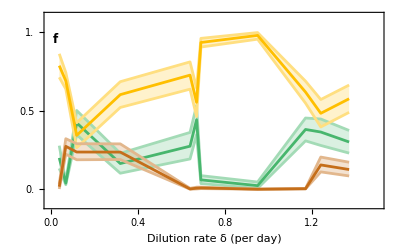

```mathematica
aicPlotComp=ListLinePlot[{lowerFoldComp,upperFoldComp,meanFoldComp,lowerHopfComp,upperHopfComp,meanHopfComp,lowerNullComp,upperNullComp,meanNullComp},
LabelStyle->ls,
InterpolationOrder->1,
Filling->{3->{1},3->{2},6->{4},6->{5},9->{7},9->{8}},
PlotRange->{{0,1.5},{-0.1,1.1}},
PlotStyle->{{Lighter[aicCols[[1]],0.5],Thickness[lt]},{Lighter[aicCols[[1]],0.5],Thickness[lt]},{aicCols[[1]],Thickness[lt]},
{Lighter[aicCols[[2]],0.5],Thickness[lt]},{Lighter[aicCols[[2]],0.5],Thickness[lt]},{aicCols[[2]],Thickness[lt]},
{Lighter[aicCols[[3]],0.5],Thickness[lt]},{Lighter[aicCols[[3]],0.5],Thickness[lt]},{aicCols[[3]],Thickness[lt]}},
Frame->{{True,True},{True,True}},
FrameLabel->{{"",""},{"Dilution rate δ (per day)",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Epilog->{Directive[{Black}],Text[Style["f",labelLetterSize,Bold],labelLetterPos]}]
```

## Grid all plots together

```mathematica
lHeight1=0.148;
lHeight2=2.931;
```

### Dimensions of Figure

```mathematica
cm=72/2.54;
```

```mathematica
(* Horizontal dimensions *)
leftPad=1.6cm;
widthFig=10cm;
rightPad=1.6cm;
(* Total horizontal dimension *)
imWidth=widthFig+leftPad+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightFig=2.2cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=0.7cm;
(* Total vertical dimension *)
imHeight=4*heightFig+heightBif+4*gapVert+bottomPad+topPad;
imHeight/cm
imWidth/cm
```

16.2

13.2

### Construct figure

```mathematica
lineBase=bottomPad;
lineTop=bottomPad+4*heightFig+heightBif+4*gapVert;
```

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[aicPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{bottomPad,0}}],{0,0},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig+bottomPad}],
(* 2nd row *)
Inset[Show[aicPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+heightFig+gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 4th row *)
Inset[Show[varSmaxPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+2*heightFig+2*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 5th row  *)
Inset[Show[varSmaxPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,0}}],{0,bottomPad+3*heightFig+3*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightFig}],
(* 6th (top) row  *)
Inset[Show[bifPlotChlor,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,bottomPad+4*heightFig+4*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
Inset[Show[bifPlotBrach,AspectRatio->Full,ImagePadding->{{leftPad,rightPad},{1,topPad}}],{0,bottomPad+4*heightFig+4*gapVert},{Left,Bottom},{widthFig+leftPad+rightPad,heightBif+topPad}],
(* Grey coloumns and labels *)
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{3.8cm,lineBase},{(3.8+2.1)cm,lineTop}],
Opacity[0.1],Directive[Darker[Black,0.6]],Rectangle[{(9.4+0.05)cm,lineBase},{(9.4-0.05)cm,lineTop}],
Opacity[1],Text[Style["H1",Black,12],{4.9cm,lineTop+0.3cm}],Text[Style["H2",Black,12],{9.4cm,lineTop+0.3cm}]
},
ImageSize->{imWidth,imHeight}
]
```

-Graphics-

### Export Figure

```mathematica
(*Export["figures/finals/fussmann_ews2.png",plotGrid,ImageResolution->300];*)
```